#### ConceptualComputational

## Straight lines

### Formatting

```mathematica
DarkGreen:=Green//Darker//Darker
```

```mathematica
labelst[str_]:=Style[str,14,FontFamily->"Arial",Background->White]
```

```mathematica
myn[n_]:=labelst[If[Abs[n]<.0001,NumberForm[0.0,4],NumberForm[n,4]]]
```

```mathematica
myn[8.0^-5]
```

0.

```mathematica
Head[myn[8.9]]
```

Style

```mathematica
labelst[cu["a"]//TraditionalForm]
```

a^3-a

```mathematica
Remove[fsty]
```

```mathematica
fsty[f_,x_]:=Text[labelst[f[x]]//TraditionalForm]
```

```mathematica
fsty[cu,"a"]
```

a^3-a

### Point-slope form

```mathematica
ptsl[m_,p_,x_]:=m x+ p[[2]]-m p[[1]]
```

```mathematica
ptsl[m_,p_,x_]:=m (x-p[[1]])+ p[[2]]//Simplify
```

```mathematica
ptsl[3,{1,2},x]
```

-1+3 x

### Two-point form

```mathematica
tpl[p_,q_,x_]:=(p[[2]]-q[[2]])/(p[[1]]-q[[1]])(x-p[[1]])+p[[2]]//Simplify
```

```mathematica
tpl[{1,2},{0,-1},x]
```

-1+3 x

```mathematica
tpl[{0,-1},{1,2},x]
```

-1+3 x

```mathematica
tpl[{1,4},{5,2},x]
```

(9-x)/2

### Intersection of projections

Given two points, find intersection of horizontal line through one point and vertical line through the other

```mathematica
wh[{a1_,a2_},{b1_,b2_}]:={b1,a2}
```

```mathematica
wh[{.3,.5},{.8,.6}]
```

{0.8,0.5}

## Definitions

### Definitions

```mathematica
cu[x_]:=x^3-x;cud[x_]:=cu'[x]
```

```mathematica
labelst[str_]:=Style[str,14,FontFamily->"Arial",Background->White];
tline[a_,x_]:=ptsl[cud[a],{a,cu[a]},x];
(*offs:=.3;*)
u[x_,offs_]:={x+offs,ptsl[cud[x],{x,cu[x]},x+offs]};
v[x_,offs_]:={x-offs,ptsl[cud[x],{x,cu[x]},x-offs]};
corner[x_,offs_]:={v[x,offs][[1]],u[x,offs][[2]]};
secline[a_,b_,x_]:=If[
a==b,
ptsl[cud[a],{a,cu[a]},x],
tpl[{a,cu[a]},{b,cu[b]},x]
]
```

```mathematica
corner[.8,.3]
```

{0.5,-0.012}

```mathematica
corner[x,.3]
```

{-0.3+x,-0.3-1. x+0.9 x^2+x^3}

```mathematica
secline[.9,1.2,x]
```

-2.268+2.33 x

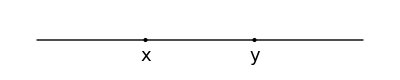

```mathematica
Graphics[{Thick,PointSize[Large],
Line[{{0,0},{3,0}}],
Point[{1,0}],Point[{2,0}],Inset[Style[x,18],{1,-.1}],Inset[Style[y,18],{2,-.1}]
},
PlotRange->{{0,3},{-.2,.2}}
]
```